# Упражнение 9. Метод на най-малките квадрати

### 1 зад. В таблицата са дадени данни за това как нивото на въглеродния диоксид в атмосферата се е изменяло в периода 1980-2000

година | 1980 | 1982 | 1984 | 1986 | 1988 | 1990 | 1992 | 1994 | 1996 | 1998 | 2000
CO_2 | 338.7 | 341.1 | 344.4 | 347.2 | 351.5 | 354.2 | 356.4 | 358.9 | 362.6 | 366.6 | 369.4

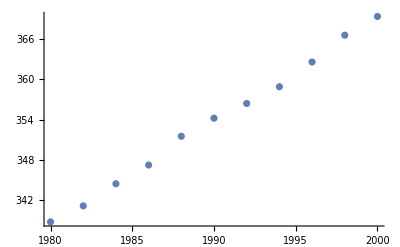

```mathematica
years = {1980,1982,1984,1986,1988,1990,1992,1994,1996,1998,2000};
co2 = {338.7,341.1,344.4,347.2,351.5,354.2,356.4,358.9,362.6,366.6,369.4};
data = ListPlot[Transpose[{years,co2}]]
```

### 2 зад. Следната таблица съдържа данни за това как се изменя броя на транзисторите в един процесор в хиляди в зависимост от годината:

година | 1971 | 1972 | 1974 | 1978 | 1982 | 1985 | 1989 | 1993 | 1997 | 1999 | 2000
бр.(x1000) | 2.25 | 2.5 | 5 | 29 | 120 | 275 | 1180 | 3100 | 7500 | 24000 | 42000

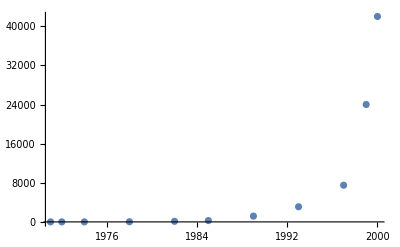

```mathematica
years = {1971,1972,1974,1978,1982,1985,1989,1993,1997,1999,2000};processors ={2.25,2.5,5,29,120,275,1180,3100,7500,24000,42000};
data=ListPlot[Transpose[{years,processors}]]
```

### 3 зад. Топка е пусната от височина 450m. Нейната височина е измервана през интервали от 1 сек. и резултатите са поместени в таблицата

t, sec | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
h, m | 450 | 445 | 431 | 408 | 375 | 332 | 279 | 216 | 143 | 61

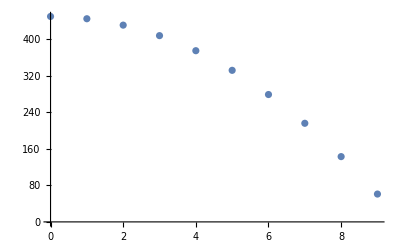

```mathematica
t={0,1,2,3,4,5,6,7,8,9};
h={450,445,431,408,375,332,279,216,143,61};
data = ListPlot[Transpose[{t,h}]]
```